```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

XXX Elements input

Nodes

```mathematica
{Nu,Nv,Nw}={20,20,2};
```

{Nu, Nv, Nw} 这里要双数

```mathematica
{Xmin,Xmax}={1/10,Pi};
{Ymin,Ymax}={1/10,Pi};
{Zmin,Zmax}={0,1/10};
```

min 和max 不能用小数，要用分式或者Pi

```mathematica
{SizeX,SizeY,SizeZ}={(Xmax-Xmin)/Nu,(Ymax-Ymin)/Nv,(Zmax-Zmin)/Nw}
```

{1/20 (-1/10+π),1/20 (-1/10+π),1/20}

```mathematica
nNodesLayerBot=1+2 Nv+Nu (2+3 Nv)
nNodesLayerMid=(Nu+1)(Nv+1)
```

1281

441

密集节点层与 中间层的数目

```mathematica
{nLayerBot,nLayerMid}={Nw+1,Nw}
```

{3,2}

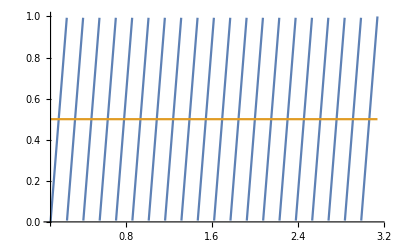

```mathematica
Plot[{FractionalPart[(y-Ymin)/SizeY+0/SizeZ],0.5},{y,Ymin,Ymax}]
```

Node of Layer1

```mathematica
Table[(1/2+FractionalPart[(y-Ymin)/SizeY+0/SizeZ]),{y,Ymin,Ymax,(1/2+FractionalPart[0/SizeZ])SizeY}]
```

{1/2,1,1/2,1,1/2,1,1/2,1,1/2,1,1/2,1,1/2,1,1/2,1,1/2,1,1/2,1,1/2,1,1/2,1,1/2,1,1/2,1,1/2,1,1/2,1,1/2,1,1/2,1,1/2,1,1/2,1,1/2}

```mathematica
Table[Table[{x,y},{x,Xmin,Xmax,(1/2+FractionalPart[(y-Ymin)/SizeY+0/SizeZ])SizeX}],{y,Ymin,Ymax,(1/2+FractionalPart[0/SizeZ])SizeY}];
Nodes=Flatten[%,1]//N;
```

```mathematica
nNodes=Dimensions[Nodes][[1]]
```

1281

```mathematica
Table[Text[n,{Nodes[[n,1]],Nodes[[n,2]],0}],{n,1,nNodes}];
txtNodes=Graphics3D[%]
```

-Graphics3D-

Node of Layer2

```mathematica
Table[Table[{x,y},{x,Xmin,Xmax,(1/2+FractionalPart[(y-Ymin)/SizeY+(0.5SizeZ)/SizeZ])SizeX}],{y,Ymin,Ymax,(1/2+FractionalPart[(0.5SizeZ)/SizeZ])SizeY}];
Nodes=Flatten[%,1]//N;
```

```mathematica
nNodes=Dimensions[Nodes][[1]]
```

441

```mathematica
Table[Text[n,{Nodes[[n,1]],Nodes[[n,2]],0}],{n,1,nNodes}];
txtNodes=Graphics3D[%]
```

-Graphics3D-

All nodes

```mathematica
Table[Table[Table[{x,y,z},{x,Xmin,Xmax,(1/2+FractionalPart[(y-Ymin)/SizeY+z/SizeZ])SizeX}],{y,Ymin,Ymax,(1/2+FractionalPart[z/SizeZ])SizeY}],{z,Zmin,Zmax,SizeZ/2}];
Nodes=Flatten[%,2]//N;
```

```mathematica
nNodes=Dimensions[Nodes][[1]]
```

4725

```mathematica
nNodesLayerBot*nLayerBot+nNodesLayerMid*nLayerMid
```

4725

```mathematica
If[nNodes==nNodesLayerBot*nLayerBot+nNodesLayerMid*nLayerMid ,True,False]
```

True

True 才能进行下一步，不然要检查网格

```mathematica
Table[Text[n,{Nodes[[n,1]],Nodes[[n,2]],Nodes[[n,3]]}],{n,1,nNodes}];
txtNodes=Graphics3D[%];
```

```mathematica
OptNodes=Table[Flatten[{ii,Nodes[[ii]]},1],{ii,1,nNodes}]
```

{{1,0.1,0.1,0.},{2,0.17604,0.1,0.},4722,{4725,3.14159,3.14159,0.1}}
 |  |  |  |

Elements [eleNumber, node1,...,node20]

Nodes on the first line, y= 0

```mathematica
k1=2Nu+1
```

41

Nodes on the first line plus second line, y = 1/2 SizeY

```mathematica
k2=k1+Nu+1
```

62

Node 1 - 4

```mathematica
Node1to4={2i-1+k2(j-1),2i+1+k2(j-1),2i+1+k2(j),2i-1+k2(j)}+(LL-1)(nNodesLayerMid+nNodesLayerBot);
```

Node 5-8

```mathematica
Node5to8={2i-1+k2(j-1),2i+1+k2(j-1),2i+1+k2(j),2i-1+k2(j)}+nNodesLayerMid+nNodesLayerBot+(LL-1)(nNodesLayerMid+nNodesLayerBot);
```

Node 9-12

```mathematica
Node9to12={2i+k2(j-1),i+1+k2(j-1)+k1,2i+k2(j),i+k2(j-1)+k1}+(LL-1)(nNodesLayerMid+nNodesLayerBot);
```

Node 13-16

```mathematica
Node13to16={2i+k2(j-1),i+1+k2(j-1)+k1,2i+k2(j),i+k2(j-1)+k1}+nNodesLayerMid+nNodesLayerBot+(LL-1)(nNodesLayerMid+nNodesLayerBot);
```

Node 17-20

```mathematica
Node17to20={(Nu+1)(j-1)+i,(Nu+1)(j-1)+i+1,(Nu+1)(j)+i+1,(Nu+1)(j)+i}+nNodesLayerBot+(LL-1)(nNodesLayerMid+nNodesLayerBot);
```

```mathematica
Join[Node1to4,Node5to8,Node9to12,Node13to16,Node17to20];
```

```mathematica
Table[Table[Join[{Nu(j-1)+i+Nu*Nv*(LL-1)},Node1to4,Node5to8,Node9to12,Node13to16,Node17to20],{j,1,Nv},{i,1,Nu}],{LL,1,Nw}];
OptElements=Flatten[%,2]
```

{{1,1,3,65,63,1723,1725,1787,1785,2,43,64,42,1724,1765,1786,1764,1282,1283,1304,1303},798,{800,2939,17,3444,3443}}
 |  |  |  |

Dummy element

```mathematica
(*OffsetEle=1000000;*)
```

```mathematica
(*Table[Table[Join[{Nu(j-1)+i+Nu*Nv*(LL-1)+OffsetEle},Node1to4,Node5to8,Node9to12,Node13to16,Node17to20],{j,1,Nv},{i,1,Nu}],{LL,1,Nw}];
DummyElements=Flatten[%,2]*)
```

Visualization

```mathematica
ElementNumber=Nu*Nv*Nw
```

800

```mathematica
Table[Join[Table[{OptNodes[[OptElements[[ee,nn]],2]],OptNodes[[OptElements[[ee,nn]],3]],OptNodes[[OptElements[[ee,nn]],4]]},{nn,2,5}],Table[{OptNodes[[OptElements[[ee,nn]],2]],OptNodes[[OptElements[[ee,nn]],3]],OptNodes[[OptElements[[ee,nn]],4]]},{nn,6,9}]],{ee,1,ElementNumber}];
Hexa=Graphics3D[{Opacity[0.8],Hexahedron[%]}]
```

-Graphics3D-

Add node number

```mathematica
Show[Hexa,txtNodes];
```

Boundary Conditions

```mathematica
BotMid=k2*Nv/2+(Nu+1)
```

641

```mathematica
BotRight=BotMid+(Nu)
```

661

```mathematica
TopMid=(Nw)(nNodesLayerMid+nNodesLayerBot)+BotMid
```

4085

```mathematica
BotNodes=
```

```mathematica
TopNodes=
```

```mathematica
SymZNodes=
```

```mathematica
SymXNodes=
```

```mathematica
Amp1Nodes=
```

```mathematica
Amp2Nodes=
```

Add segment because inp file can have maximum 16 items in one line
Use Null, otherwise use Nothing

```mathematica
Table[Table[{Join[{Nu(j-1)+i+Nu*Nv*(LL-1)},Node1to4,Node5to8,{Null}],Join[Node9to12,Node13to16,Node17to20]},{j,1,Nv},{i,1,Nu}],{LL,1,Nw}];
IntOptElements=Flatten[%,3]
```

{{1,1,3,65,63,1723,1725,1787,1785,Null},1598,{2940,2962,3002,2961,4662,4684,4724,4683,3422,3423,3444,3443}}
 |  |  |  |

```mathematica
(*Table[Table[{Join[{Nu(j-1)+i+Nu*Nv*(LL-1)+OffsetEle},Node1to4,Node5to8,{Null}],Join[Node9to12,Node13to16,Node17to20]},{j,1,Nv},{i,1,Nu}],{LL,1,Nw}];
IntDummyElements=Flatten[%,3]*)
```

```mathematica
Nu*Nv*Nw
```

800

```mathematica
Export["Mma800Element.csv",Join[{{"nodes",nNodes}},OptNodes,{{"elements",Nu*Nv*Nw}},IntOptElements,{{"Dummy elements",Nu*Nv*Nw}},(*IntDummyElements,*){{"*Nset, nset=BotNodes","generate"},{1,nNodesLayerBot,1}},{{"*Nset, nset=TopNodes"},{(Nw)(nNodesLayerMid+nNodesLayerBot),(Nw)(nNodesLayerMid+nNodesLayerBot)+nNodesLayerBot,1}},{{"*Nset, nset=BotMid"},{BotMid}},{{"*Nset, nset=BotRight"},{BotRight}},{{"*Nset, nset=TopMid"},{TopMid}}]];
```